# HW 7 - ASTR501 Created with Wolfram Mathematica 11.1.0 on March 21, 2017

## Daniel George - dgeorge5@illinois.edu

### Initialization

```mathematica
SetOptions[Plot,{Frame->True,FrameLabel->{"ν (Hz)","T_B (K)"},Filling->Bottom,ImageSize->400}];
Unprotect@Quantity;Quantity[0.,_]=Quantity[0,_]=0;Protect@Quantity;
```

### a)

```mathematica
ν0=Quantity[115.272, "Gigahertz"];
sB=Solve[Quantity[, "PlanckConstant"]ν0==Quantity[, "BoltzmannConstant"]B J(J+1)/2-0/.J->1,B][[1,1]]//UnitConvert
```

B→5.53219 K

### b)

```mathematica
g[j_]:=2j+1;f[T_][j_]:=g[j]Exp[- B /T j(j+1)/2]/Sum[g[i]Exp[- B i(i+1)/2/T],{i,0,10}]/.sB;
#->f@Quantity[10, "Kelvins"]/@#&@{0,1,2}//Thread
```

{0→0.252014,1→0.434797,2→0.239671}

### c)

```mathematica
CO[n_]=Quiet@Solve[ {nCO==.2nC,nH/nC==LinguisticAssistant/LinguisticAssistant} /.nH->2 n/Quantity[, ("Centimeters")^3],{nCO,nC}][[1,1,2]];CO@50
```

6451.61 per meter^3

### d)

```mathematica
sV=Solve[3 1/2 LinguisticAssistant vx^2==3/2 Quantity[, "BoltzmannConstant"]Quantity[10, "Kelvins"],vx][[2,1]]
```

vx→54.483 m/s

### e)

#### Line profile function

```mathematica
νc=(1-vz/Quantity[, "SpeedOfLight"])ν0;
ϕ=Exp[-(ν-νc)^2/(2 σ^2)]/(√(2π) σ);
```

#### Frequency width

```mathematica
σν[v_]:=v/Quantity[, "SpeedOfLight"]ν0;
```

#### Einstein’s coefficients

```mathematica
A21=LinguisticAssistant;
```

```mathematica
B21=Solve[A21==2 Quantity[, "PlanckConstant"]ν0^3/Quantity[, "SpeedOfLight"]^2 b21,b21][[1,1,2]]
```

3.17293×10^9 s/kg

```mathematica
B12=Solve[g@0 b12==g@1 B21,b12][[1,1,2]]
```

9.51879×10^9 s/kg

#### Emissivity

```mathematica
n@i_:=f[T][i-1] CO[nH];
jν[nH_,vz_,T_,σ_]=n@2 A21 Quantity[, "PlanckConstant"] ν/(4 π) ϕ;
```

### f) Absorptivity

```mathematica
αν[nH_,vz_,T_,σ_]=Quantity[, "PlanckConstant"]ν/(4π) (n@1 B12 -n@2 B21)ϕ;
```

Yes.

### g) Optical depth

```mathematica
αν[50,0,Quantity[10, "Kelvins"],σν@Quantity[1, ("Kilometers")/("Seconds")] ]Quantity[1, "Parsecs"]/.ν->ν0
```

1.27966

### h)

#### One function to solve them all (including CMB)

```mathematica
BT[nH_:50,d_:1,vz_:0,Δv_:Quantity[1, ("Kilometers")/("Seconds")],T_:Quantity[10, "Kelvins"],nH2_:0,vz2_:0,Δv2_:1,T2_:1]:=ParametricNDSolveValue[UnitConvert@{Iν'@z /Quantity[1.0, "Parsecs"]==-(αν[nH,vz,T,σν@Δv]+αν[nH2,vz2,T2,σν@Δv2]) Iν[ z]+(jν[nH,vz,T,σν@Δv]+jν[nH2,vz2,T2,σν@Δv2]),Iν[-d]==2 Quantity[, "PlanckConstant"]ν^3/Quantity[, "SpeedOfLight"]^2/(Exp[Quantity[, "PlanckConstant"]ν/(Quantity[, "BoltzmannConstant"]Quantity[2.725, "Kelvins"])]-1)}/.Quantity[x_,_]:>x, QuantityMagnitude@UnitConvert[Quantity[, "SpeedOfLight"]^2/(2 Quantity[, "BoltzmannConstant"])/ν^2]Iν@0 ,{z,-d,0 },ν]
```

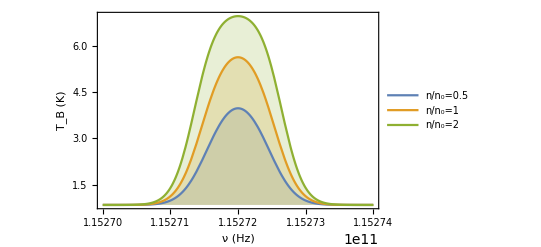

```mathematica
Plot[Evaluate@Table[BT[i 50]@x,{i,{.5,1,2}}],{x,115.27 10^9,115.274 10^9},PlotLegends->{"n/n_0=0.5","n/n_0=1","n/n_0=2"}]
```

### i)

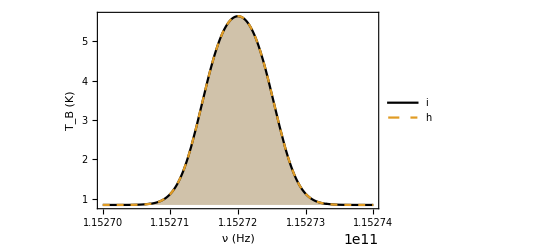

```mathematica
Plot[Evaluate@{BT[50/(2 √(2π))(Exp[-(z+5 )^2/2]+Exp[-(z+8 )^2/2]),16]@x,BT[]@x},{x,115.27 10^9,115.274 10^9},PlotStyle->{Black,Dashed},PlotLegends->{"i","h"}]
```

No. They look identical.

### j)

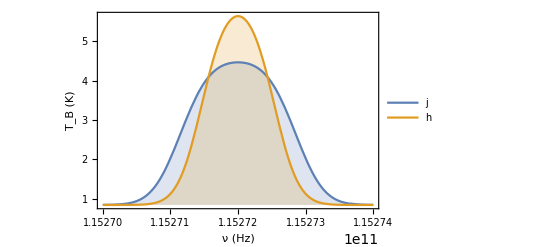

```mathematica
Plot[Evaluate@{BT[50,1,1.5 Sin[2π z]Quantity[1, ("Kilometers")/("Seconds")]]@x,BT[]@x},{x,115.27 10^9,115.274 10^9},PlotLegends->{"j","h"}]
```

Yes. They can be distinguished.

### k)

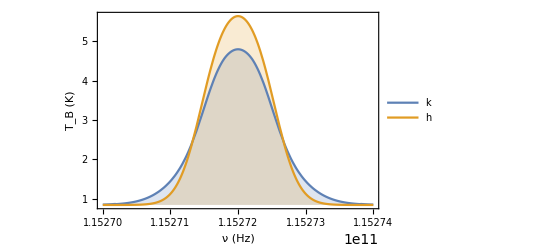

```mathematica
Plot[Evaluate@{BT[50/(2 √(2π))Exp[-(z+8)^2/2],16,0,Quantity[1.5, ("Kilometers")/("Seconds")],Quantity[12, "Kelvins"],50/(2 √(2π))Exp[-(z+5)^2/2],0,Quantity[.8, ("Kilometers")/("Seconds")] ,Quantity[8, "Kelvins"]]@x,BT[]@x},{x,115.27 10^9,115.274 10^9},PlotLegends->{"k","h"}]
```

### Extra

Yes, I did. I should since the CMB brightness temperature would be comparable to the brightness temperatures we got. It shifts everything up by about 1 K. Furthermore, it changes the relative difference between the two curves in part k)